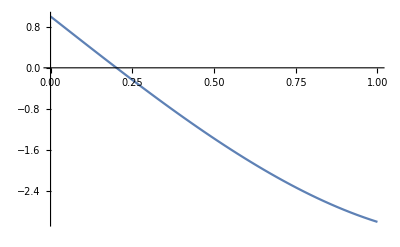

```mathematica
BisectionMWE[a0_,b0_,error_,f_]:=
Module[{},a=N[a0];b=N[b0];m=(a+b)/2;
i=0;If[f[a]*f[b]>0,Print["We cannot continue with Bisection Method"];Return[]];
Output={{i,a,m,b,(b-a)/2}};
While[Abs[b-a]>2error,If[Sign[f[a]]==Sign[f[m]],a=m,b=m];
m=(a+b)/2;i++;
Output=Append[Output,{i,a,m,b,(b-a)/2}];];
Print[NumberForm[TableForm[Output,
TableHeadings->{None,{"i","ai","mi","bi","(bi-ai)/2"}}],8]];
Print["Number of iterations required to achieve desired accuracy= ",i];
Print["Root after ",i,"iterations = ",NumberForm[m,8]];
Print["Functions value at approximated root, f[m]= ",NumberForm[f[m],8]];];
f[x_]:=x^3-5x+1;
error=10^(-2);
a=0;b=1;
Plot[f[x],{x,0,1}]
```

```mathematica
BisectionMWE[a,b,error,f]
```

i | ai | mi | bi | (bi-ai)/2
0 | 0. | 0.5 | 1. | 0.5
1 | 0. | 0.25 | 0.5 | 0.25
2 | 0. | 0.125 | 0.25 | 0.125
3 | 0.125 | 0.1875 | 0.25 | 0.0625
4 | 0.1875 | 0.21875 | 0.25 | 0.03125
5 | 0.1875 | 0.203125 | 0.21875 | 0.015625
6 | 0.1875 | 0.1953125 | 0.203125 | 0.0078125

Number of iterations required to achieve desired accuracy= 6

Root after 6iterations = 0.1953125

Functions value at approximated root, f[m]= 0.030888081

```mathematica
f[x_]:=x^3-5x+1;
error=10^(-4);
a=0;b=1;
BisectionMWE[a,b,error,f]
```

i | ai | mi | bi | (bi-ai)/2
0 | 0. | 0.5 | 1. | 0.5
1 | 0. | 0.25 | 0.5 | 0.25
2 | 0. | 0.125 | 0.25 | 0.125
3 | 0.125 | 0.1875 | 0.25 | 0.0625
4 | 0.1875 | 0.21875 | 0.25 | 0.03125
5 | 0.1875 | 0.203125 | 0.21875 | 0.015625
6 | 0.1875 | 0.1953125 | 0.203125 | 0.0078125
7 | 0.1953125 | 0.19921875 | 0.203125 | 0.00390625
8 | 0.19921875 | 0.20117188 | 0.203125 | 0.001953125
9 | 0.20117188 | 0.20214844 | 0.203125 | 0.0009765625
10 | 0.20117188 | 0.20166016 | 0.20214844 | 0.00048828125
11 | 0.20117188 | 0.20141602 | 0.20166016 | 0.00024414063
12 | 0.20141602 | 0.20153809 | 0.20166016 | 0.00012207031
13 | 0.20153809 | 0.20159912 | 0.20166016 | 0.000061035156

Number of iterations required to achieve desired accuracy= 13

Root after 13iterations = 0.20159912

Functions value at approximated root, f[m]= 0.00019782746

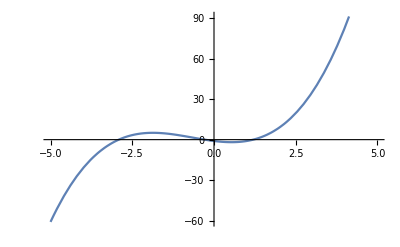

```mathematica
f[x_]:=x^3+2x^2-3x-1;
error=10^(-5);
a=1;b=2;
Plot[f[x],{x,-5,5}]
```

```mathematica
BisectionMWE[a,b,error,f]
```

i | ai | mi | bi | (bi-ai)/2
0 | 1. | 1.5 | 2. | 0.5
1 | 1. | 1.25 | 1.5 | 0.25
2 | 1. | 1.125 | 1.25 | 0.125
3 | 1.125 | 1.1875 | 1.25 | 0.0625
4 | 1.1875 | 1.21875 | 1.25 | 0.03125
5 | 1.1875 | 1.203125 | 1.21875 | 0.015625
6 | 1.1875 | 1.1953125 | 1.203125 | 0.0078125
7 | 1.1953125 | 1.1992188 | 1.203125 | 0.00390625
8 | 1.1953125 | 1.1972656 | 1.1992188 | 0.001953125
9 | 1.1972656 | 1.1982422 | 1.1992188 | 0.0009765625
10 | 1.1982422 | 1.1987305 | 1.1992188 | 0.00048828125
11 | 1.1982422 | 1.1984863 | 1.1987305 | 0.00024414063
12 | 1.1984863 | 1.1986084 | 1.1987305 | 0.00012207031
13 | 1.1986084 | 1.1986694 | 1.1987305 | 0.000061035156
14 | 1.1986694 | 1.1987 | 1.1987305 | 0.000030517578
15 | 1.1986694 | 1.1986847 | 1.1987 | 0.000015258789
16 | 1.1986847 | 1.1986923 | 1.1987 | 7.6293945×10^-6

Number of iterations required to achieve desired accuracy= 16

Root after 16iterations = 1.1986923

Functions value at approximated root, f[m]= 6.5831663×10^-6

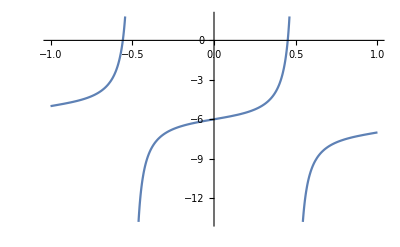

```mathematica
f[x_]:=Tan[Pi x]-x-6;
error=5*10^(-5);
Plot[f[x],{x,-1,1}]
```

```mathematica
BisectionMWE[0,0.5,error,f]
```

i | ai | mi | bi | (bi-ai)/2
0 | 0. | 0.25 | 0.5 | 0.25
1 | 0.25 | 0.375 | 0.5 | 0.125
2 | 0.375 | 0.4375 | 0.5 | 0.0625
3 | 0.4375 | 0.46875 | 0.5 | 0.03125
4 | 0.4375 | 0.453125 | 0.46875 | 0.015625
5 | 0.4375 | 0.4453125 | 0.453125 | 0.0078125
6 | 0.4453125 | 0.44921875 | 0.453125 | 0.00390625
7 | 0.44921875 | 0.45117188 | 0.453125 | 0.001953125
8 | 0.44921875 | 0.45019531 | 0.45117188 | 0.0009765625
9 | 0.45019531 | 0.45068359 | 0.45117188 | 0.00048828125
10 | 0.45068359 | 0.45092773 | 0.45117188 | 0.00024414063
11 | 0.45092773 | 0.4510498 | 0.45117188 | 0.00012207031
12 | 0.45092773 | 0.45098877 | 0.4510498 | 0.000061035156
13 | 0.45098877 | 0.45101929 | 0.4510498 | 0.000030517578

Number of iterations required to achieve desired accuracy= 13

Root after 13iterations = 0.45101929

Functions value at approximated root, f[m]= -0.0037148206